# Уравнения математической физики

## Лектор: Корзюк Виктор Иванович, академик

## Преподаватель: Кулешов Александр Аркадьевич, аудитория 407

Студентка 9 группы 4 курса Харитонова Вероника Ренальдовна

## Лабораторная группа по формуле Даламбера и Кирхгофа

Задача №1. Решить задачу Коши

(∂^2 u)/(∂t^2)-(∂^2 u)/(∂x^2)=6

∂_t u=4x при t=0

u=x^2 при t=0

a=1

Решение ищем по формуле Даламбера:

```mathematica
u[x_,t_]=1/2((x+t)^2+(x-t)^2)+1/2∫_(x-t)^(x+t) 4ξⅆξ+1/2∫_0^t ∫_(x-(t-τ))^(x+(t-τ)) 6ⅆξⅆτ//FullSimplify
```

(2 t+x)^2

Проверка:

```mathematica
D[u[x,t], t,t]-D[u[x,t], x,x]
```

6

```mathematica
u[x,0]
```

x^2

```mathematica
D[u[x,t], t]/.{t->0}
```

4 x

Задача №2. Решить задачу Коши

(∂^2 u)/(∂t^2)-4(∂^2 u)/(∂x^2)=x t

∂_t u=x при t=0

u=x^2 при t=0

a=2

Решение ищем по формуле Даламбера:

```mathematica
u[x_,t_]=1/2((x+2t)^2+(x-2t)^2)+1/4∫_(x-2t)^(x+2t) ξⅆξ+1/4∫_0^t ∫_(x-2(t-τ))^(x+2(t-τ)) ξ τⅆξⅆτ//FullSimplify
```

4 t^2+t x+(t^3 x)/6+x^2

Проверка:

```mathematica
D[u[x,t], t,t]-4 D[u[x,t], x,x]
```

t x

```mathematica
u[x,0]
```

x^2

```mathematica
D[u[x,t], t]/.{t->0}
```

x

Задача №3. Решить задачу Коши

(∂^2 u)/(∂t^2)-(∂^2 u)/(∂x^2)=Sin[x]

∂_t u=0 при t=0

u=Sin[x] при t=0

a=1

Решение ищем по формуле Даламбера:

```mathematica
u[x_,t_]=1/2(Sin[x+t]+Sin[x-t])+1/2∫_(x-t)^(x+t) 0ⅆξ+1/2∫_0^t ∫_(x-(t-τ))^(x+(t-τ)) Sin[ξ]ⅆξⅆτ//FullSimplify
```

Sin[x]

Проверка:

```mathematica
D[u[x,t], t,t]-D[u[x,t], x,x]
```

Sin[x]

```mathematica
u[x,0]
```

Sin[x]

```mathematica
D[u[x,t], t]/.{t->0}
```

0

Задача №4. Решить задачу Коши

(∂^2 u)/(∂t^2)-(∂^2 u)/(∂x^2)=ⅇ^x

∂_t u=Cos[x]+x при t=0

u=Sin[x] при t=0

a=1

Решение ищем по формуле Даламбера:

```mathematica
u[x_,t_]=1/2(Sin[x+t]+Sin[x-t])+1/2∫_(x-t)^(x+t) (Cos[ξ]+ξ)ⅆξ+1/2∫_0^t ∫_(x-(t-τ))^(x+(t-τ)) ⅇ^ξ ⅆξⅆτ//FullSimplify
```

t x+ⅇ^x (-1+Cosh[t])+Sin[t+x]

Проверка:

```mathematica
D[u[x,t], t,t]-D[u[x,t], x,x]//FullSimplify
```

ⅇ^x

```mathematica
u[x,0]
```

Sin[x]

```mathematica
D[u[x,t], t]/.{t->0}
```

x+Cos[x]

Задача №5. Решить задачу Коши

(∂^2 u)/(∂t^2)-9(∂^2 u)/(∂x^2)=Sin[x]

∂_t u=1 при t=0

u=1 при t=0

a=3

Решение ищем по формуле Даламбера:

```mathematica
u[x_,t_]=1+1/6∫_(x-3t)^(x+3t) 1ⅆξ+1/6∫_0^t ∫_(x-3(t-τ))^(x+3(t-τ)) Sin[ξ]ⅆξⅆτ//FullSimplify
```

1+t+2/9 Sin[(3 t)/2]^2 Sin[x]

Проверка:

```mathematica
D[u[x,t], t,t]-9 D[u[x,t], x,x]//FullSimplify
```

Sin[x]

```mathematica
u[x,0]
```

1

```mathematica
D[u[x,t], t]/.{t->0}
```

1

Задача №6. Решить задачу Коши

(∂^2 u)/(∂t^2)-a^2(∂^2 u)/(∂x^2)=Sin[ωx]

∂_t u=0 при t=0

u=0 при t=0

a=a

Решение ищем по формуле Даламбера:

```mathematica
u[x_,t_]=1/(2a)∫_(x-at)^(x+at) 0ⅆξ+1/(2a)∫_0^t ∫_(x-a(t-τ))^(x+a(t-τ)) Sin[ω ξ]ⅆξⅆτ//FullSimplify
```

-((-1+Cos[a t ω]) Sin[x ω])/(a^2 ω^2)

Проверка:

```mathematica
D[u[x,t], t,t]-a^2 D[u[x,t], x,x]//FullSimplify
```

Sin[x ω]

```mathematica
u[x,0]
```

0

```mathematica
D[u[x,t], t]/.{t->0}
```

0

Задача №7. Решить задачу Коши

(∂^2 u)/(∂t^2)-a^2(∂^2 u)/(∂x^2)=Sin[ωt]

∂_t u=0 при t=0

u=0 при t=0

a=a

Решение ищем по формуле Даламбера:

```mathematica
u[x_,t_]=1/(2a)∫_(x-at)^(x+at) 0ⅆξ+1/(2a)∫_0^t ∫_(x-a(t-τ))^(x+a(t-τ)) Sin[ω τ]ⅆξⅆτ//FullSimplify
```

(t ω-Sin[t ω])/ω^2

Проверка:

```mathematica
D[u[x,t], t,t]-a^2 D[u[x,t], x,x]//FullSimplify
```

Sin[t ω]

```mathematica
u[x,0]
```

0

```mathematica
D[u[x,t], t]/.{t->0}
```

0

Задача №8. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=2

∂_t u=y при t=0

u=x при t=0

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x;
ψ[x_,y_,z_]=y;
a=1;
f[x_,y_,z_,t_]=2;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

x+t (t+y)

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//FullSimplify
```

2

```mathematica
u[0,x,y,z]
```

x

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

y

Задача №9. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=6x y t

∂_t u=x y при t=0

u=x^2-y^2  при t=0

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x^2-y^2;
ψ[x_,y_,z_]=x y;
a=1;
f[x_,y_,z_,t_]=6 x y t;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

x^2+(t+t^3) x y-y^2

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//FullSimplify
```

6 t x y

```mathematica
u[0,x,y,z]
```

x^2-y^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

x y

Задача №10. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=x^3-3x y^2

∂_t u=ⅇ^y Sin[x] при t=0

u=ⅇ^x Cos[y] при t=0

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=ⅇ^x Cos[y];
ψ[x_,y_,z_]=ⅇ^y Sin[x];
a=1;
f[x_,y_,z_,t_]=x^3-3 x y^2;
ψ[x+a t Cos[phi]Sin[theta],y+a t Sin[phi]Sin[theta],z+a t Cos[theta]]//FullSimplify
```

ⅇ^(y+t Sin[phi] Sin[theta]) Sin[x+t Cos[phi] Sin[theta]]

```mathematica
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//FullSimplify
```

```mathematica
u[0,x,y,z]
```

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

Mathematica не справляется с решением этого примера

Задача №11. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=t Sin[y]

∂_t u=Sin[y]при t=0

u=x^2 при t=0

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x^2;
ψ[x_,y_,z_]=Sin[y];
a=1;
f[x_,y_,z_,t_]=t Sin[y];
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

```mathematica
FullSimplify[t^2+x^2+
∫_0^t 1/2(t-τ)If[t≠τ,(2Sin[Abs[t-τ]])/Abs[t-τ],Integrate[BesselJ[0,Abs[t-τ]Sin[theta]]Sin[theta],{theta,0,π},Assumptions:>t==τ]]Sin[y]ⅆτ+
1/2 t If[t≠0,(2Sin[Abs[t]])/Abs[t],Integrate[BesselJ[0,Abs[t]Sin[theta]]Sin[theta],{theta,0,π},Assumptions:>t==0]]Sin[y],{t>τ,t>0}
]
```

```mathematica
u[t_,x_,y_,z_]=t^2+x^2+t Sin[y];
```

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//Expand
```

t Sin[y]

```mathematica
u[0,x,y,z]
```

x^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

Sin[y]

Задача №12. Решить задачу Коши

(∂^2 u)/(∂t^2)-2((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=0

∂_t u=2 x^2+y^2 при t=0

u=2 x^2-y^2 при t=0

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=2 x^2-y^2;
ψ[x_,y_,z_]=2 x^2+y^2;
a=√2;
f[x_,y_,z_,t_]=0;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

2 (1+t) (t^2+x^2)+(-1+t) y^2

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-2(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//Expand
```

0

```mathematica
u[0,x,y,z]
```

2 x^2-y^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

2 x^2+y^2

Задача №13. Решить задачу Коши

(∂^2 u)/(∂t^2)-3((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=x^3+y^3

∂_t u=y^2 при t=0

u=x^2 при t=0

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x^2;
ψ[x_,y_,z_]=y^2;
a=√3;
f[x_,y_,z_,t_]=x^3+y^3;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

t^3+x^2+t y^2+3/4 t^4 (x+y)+1/2 t^2 (6+x^3+y^3)

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-3(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//Expand
```

x^3+y^3

```mathematica
u[0,x,y,z]
```

x^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

y^2

Задача №15 (замена переменных). Решить задачу Коши

(∂^2 u)/(∂t^2)-a^2((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=0

∂_t u=Sin[b x+c1 y] при t=0

u=Cos[b x+c1 y] при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
(*Needs["VectorAnalysis`"]*)
```

```mathematica
φ[x_,y_,z_]=Cos[b x + c1 y];
ψ[x_,y_,z_]=Sin[b x + c1 y];
a=a;
f[x_,y_,z_,t_]=0;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

```mathematica
FullSimplify[t^2+x^2+
∫_0^t 1/2(t-τ)If[t≠τ,(2Sin[Abs[t-τ]])/Abs[t-τ],Integrate[BesselJ[0,Abs[t-τ]Sin[theta]]Sin[theta],{theta,0,π},Assumptions:>t==τ]]Sin[y]ⅆτ+
1/2 t If[t≠0,(2Sin[Abs[t]])/Abs[t],Integrate[BesselJ[0,Abs[t]Sin[theta]]Sin[theta],{theta,0,π},Assumptions:>t==0]]Sin[y],{t>τ,t>0}
]
```

```mathematica
u[t_,x_,y_,z_]=t^2+x^2+t Sin[y];
```

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//Expand
```

t Sin[y]

```mathematica
u[0,x,y,z]
```

x^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

Sin[y]

Задача №16. Решить задачу Коши

(∂^2 u)/(∂t^2)-a^2((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=0

∂_t u=(x^2+y^2)^2 при t=0

u=(x^2+y^2)^2 при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=(x^2+y^2)^2;
ψ[x_,y_,z_]=(x^2+y^2)^2;
f[x_,y_,z_,t_]=0;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

8/15 a^4 t^4 (5+t)+8/3 a^2 t^2 (3+t) (x^2+y^2)+(1+t) (x^2+y^2)^2

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-a^2(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//FullSimplify
```

0

```mathematica
u[0,x,y,z]
```

(x^2+y^2)^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

(x^2+y^2)^2

Задача №17. Решить задачу Коши

(∂^2 u)/(∂t^2)-a^2((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2))=(x^2+y^2)ⅇ^t

∂_t u=0 при t=0

u=0при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=0;
ψ[x_,y_,z_]=0;
f[x_,y_,z_,t_]=(x^2+y^2)ⅇ^t;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

1/3 (2 a^2 (-6+6 ⅇ^t-t (6+t (3+t)))+3 (-1+ⅇ^t-t) (x^2+y^2))

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-a^2(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y])//FullSimplify
```

ⅇ^t (x^2+y^2)

```mathematica
u[0,x,y,z]
```

0

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

0

Задача №18. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2) + (∂^2 u)/(∂z^2))=2x y z

∂_t u=1 при t=0

u=x^2+y^2-2 z^2 при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x^2+y^2-2 z^2;
ψ[x_,y_,z_]=1;
f[x_,y_,z_,t_]=2 x y z;
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

t+x^2+y^2+t^2 x y z-2 z^2

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y]+D[u[t,x,y,z], z,z])//FullSimplify
```

2 x y z

```mathematica
u[0,x,y,z]
```

x^2+y^2-2 z^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

1

Задача №19. Решить задачу Коши

(∂^2 u)/(∂t^2)-8((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)+ (∂^2 u)/(∂z^2))=t^2 x^2

∂_t u=z^2 при t=0

u=y^2 при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=y^2;
ψ[x_,y_,z_]=z^2;
f[x_,y_,z_,t_]=t^2 x^2;
a=√8;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

8 t^2+(8 t^3)/3+(2 t^6)/45+(t^4 x^2)/12+y^2+t z^2

Проверка:

```mathematica
D[u[t,x,y,z], t,t]-8(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y]+D[u[t,x,y,z], z,z])//FullSimplify
```

t^2 x^2

```mathematica
u[0,x,y,z]
```

y^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

z^2

Задача №28. Решить задачу Коши

(∂^2 u)/(∂t^2) = (∂^2 u)/(∂x^2)+x Sin[t]

∂_t u=Cos[x] при t=0
u=Sin[x] при t=0

Решение ищем по формуле Даламбера

```mathematica
Clear[u,x,t,τ,ξ,g,f];
u[x_,t_] = 1/2(Sin[x-t] + Sin[x+t]) + 1/2∫_(x - t)^(x + t) Cos[ξ] ⅆξ +  1/2∫_0^t ∫_(x - (t-τ))^(x + (t-τ)) ξ Sin[τ]ⅆξⅆτ//FullSimplify
```

t x-x Sin[t]+Sin[t+x]

Проверка:

```mathematica
FullSimplify[D[u[x,t], t,t]-D[u[x,t], x,x]]
```

x Sin[t]

```mathematica
u[x,0]//FullSimplify
```

Sin[x]

```mathematica
D[u[x,t], t]/.{t->0}
```

Cos[x]

Задача №29. Решить задачу Коши

(∂^2 u)/(∂t^2) = (∂^2 u)/(∂x^2)+g[x]f[t]

∂_t u=0 при t=0
u=ϕ[x] при t=0

Решение ищем по формуле Даламбера

```mathematica
Clear[u,x,t,ϕ,τ,ξ,g,f];
u[x_,t_] = 1/2(ϕ[x-t] + ϕ[x+t]) + 1/2∫_0^t ∫_(x - (t-τ))^(x + (t-τ)) g[ξ]f[τ]ⅆξⅆτ//FullSimplify
```

1/2 (∫_0^t ∫_(-t+x+τ)^(t+x-τ) f[τ] g[ξ]ⅆξⅆτ+ϕ[-t+x]+ϕ[t+x])

Проверка:

```mathematica
FullSimplify[D[u[x,t], t,t]-D[u[x,t], x,x]]
```

f[t] g[x]

```mathematica
u[x,0]//FullSimplify
```

```mathematica
1/2 ∫_0^0 ∫_(x+τ)^(x-τ) f[ξ] g[ξ]ⅆξⅆτ+ϕ[x]
```

1/2 ∫_0^0 ∫_(x+τ)^(x-τ) f[ξ] g[ξ]ⅆξⅆτ+ϕ[x]

```mathematica
D[u[x,t], t]/.{t->0}
```

0

Задача №30. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=0

∂_t u=x^2 y^2 z^2 при t=0

u=x y z при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x y z;
ψ[x_,y_,z_]=x^2 y^2 z^2;
f[x_,y_,z_,t_]=0;
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

t^7/105+x y z+t x^2 y^2 z^2+1/15 t^5 (x^2+y^2+z^2)+1/3 t^3 (y^2 z^2+x^2 (y^2+z^2))

Проверка:

```mathematica
FullSimplify[D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y]+D[u[t,x,y,z], z,z])]
```

t^2 x^2

```mathematica
u[0,x,y,z]
```

y^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

z^2

Задача №31. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=0

∂_t u=xy  при t=0

u=r^2 при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=y^2;
ψ[x_,y_,z_]=z^2;
f[x_,y_,z_,t_]=t^2 x^2;
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

1/180 t^2 (180+t (60+t^3+15 t x^2))+y^2+t z^2

Проверка:

```mathematica
FullSimplify[D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y]+D[u[t,x,y,z], z,z])]
```

t^2 x^2

```mathematica
u[0,x,y,z]
```

y^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

z^2

Задача №32. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=0

∂_t u=x^2 - y^2   при t=0

u=ⅇ^x Cos[y]  при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=ⅇ^x Cos[y];
ψ[x_,y_,z_]=x^2 - y^2;
f[x_,y_,z_,t_]=0;
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

$Aborted

Задача №33. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=0

∂_t u=1  при t=0

u=x^2+y^2  при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x^2+y^2;
ψ[x_,y_,z_]=1;
f[x_,y_,z_,t_]=0;
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

t+2 t^2+x^2+y^2

Проверка:

```mathematica
FullSimplify[D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y]+D[u[t,x,y,z], z,z])]
```

0

```mathematica
u[0,x,y,z]
```

x^2+y^2

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

1

Задача №34. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=0

∂_t u=ⅇ^-x  при t=0

u=ⅇ^x  при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=ⅇ^x;
ψ[x_,y_,z_]=ⅇ^-x;
f[x_,y_,z_,t_]=0;
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}],Re[t]>0]
```

Cosh[t-x]+Sinh[t+x]

Проверка:

```mathematica
FullSimplify[D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y]+D[u[t,x,y,z], z,z])]
```

0

```mathematica
u[0,x,y,z]//TrigToExp
```

ⅇ^x

```mathematica
D[u[t,x,y,z], t]/.{t->0}//TrigToExp
```

ⅇ^-x

Задача №35. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=0

∂_t u=0  при t=0

u = 1/x при t = 0

x≠0

x^2 + y^2+z^2 ≠ t^2

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=1/x;
ψ[x_,y_,z_]=0;
f[x_,y_,z_,t_]=0;
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}],{x≠0,x^2 + y^2+z^2 ≠ t^2 }]
```

$Aborted

Задача №36. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=0

∂_t u=x y+z  при t=0

u=x y z  при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x y z;
ψ[x_,y_,z_]=x y + z;
f[x_,y_,z_,t_]=aa x + b t;
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

1/6 t (b t^2+3 aa t x+6 x y)+(t+x y) z

Проверка:

```mathematica
FullSimplify[D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y]+D[u[t,x,y,z], z,z])]
```

b t+aa x

```mathematica
u[0,x,y,z]
```

x y z

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

x y+z

Задача №37. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=x/(1+t^2)ⅇ^y Cos[z]

∂_t u=0 при t=0

u= z Sin[√2(x+y)] при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=z Sin[√2(x+y)] ;
ψ[x_,y_,z_]=0;
f[x_,y_,z_,t_]=x/(1+t^2)ⅇ^y Cos[z];
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}]
]
```

$Aborted

Задача №38. Решить задачу Коши

(∂^2 u)/(∂t^2)-((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)  + (∂^2 u)/(∂z^2))=(x t)/(1+t^2)

∂_t u=y Cos[z] при t=0

u=x Sin[y]  при t=0

```mathematica
Clear[a,φ,ψ,t,f,x,y,z,u];
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
φ[x_,y_,z_]=x Sin[y];
ψ[x_,y_,z_]=y Cos[z];
f[x_,y_,z_,t_]=(x t)/(1+t^2);
a=1;
u[t_,x_,y_,z_]=FullSimplify[
t/(4π)Integrate[ψ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]]*(JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}]+1/(4π)* D[t Integrate[φ[x+a t Cos[phi] Sin[theta],y+a t Sin[phi] Sin[theta], z+a t Cos[theta]] (JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],t]+
Integrate[(t-τ)/(4π)Integrate[f[x+a(t-τ)Cos[phi]Sin[theta],y+a(t-τ)Sin[phi]Sin[theta],z+a(t-τ)Cos[theta],τ](JacobianDeterminant[Spherical[r,theta,phi]]/.{r->1}),{theta,0,Pi},{phi,-Pi,Pi}],{τ,0,t}], t>0
]
```

1/2 (2 x ArcTan[t]+t x (-2+Log[1-ⅈ t]+Log[1+ⅈ t])+2 y Cos[z] Sin[t]+2 x Cos[t] Sin[y])

```mathematica
Plot3D[u[t,1,1,z],{t,.1,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
TrigFactor[(-2+Log[1-ⅈ t]+Log[1+ⅈ t])]
```

-2+Log[1-ⅈ t]+Log[1+ⅈ t]

```mathematica
FullSimplify[ComplexExpand[(-2+Log[1-ⅈ t]+Log[1+ⅈ t]),t],t>0]
```

ⅈ (2 ⅈ+Arg[1-ⅈ t]+Arg[1+ⅈ t])+Log[1+t^2]

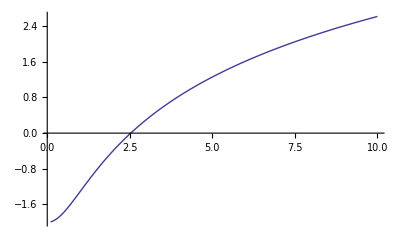

```mathematica
Plot[(-2+Log[1-ⅈ t]+Log[1+ⅈ t]), {t,.1,10}]
```

Проверка:

```mathematica
FullSimplify[D[u[t,x,y,z], t,t]-(D[u[t,x,y,z], x,x]+D[u[t,x,y,z], y,y]+D[u[t,x,y,z], z,z])]
```

(t x)/(1+t^2)

```mathematica
u[0,x,y,z]
```

x Sin[y]

```mathematica
D[u[t,x,y,z], t]/.{t->0}
```

y Cos[z]